## Variables

```mathematica
pmax=45(* max position *);
```

```mathematica
jmax=40 (* max time *);
```

```mathematica
listx= Table[p -(pmax+1),{p,1,2pmax+1}]  (* argument = integer variable *)
```

{-45,-44,-43,-42,-41,-40,-39,-38,-37,-36,-35,-34,-33,-32,-31,-30,-29,-28,-27,-26,-25,-24,-23,-22,-21,-20,-19,-18,-17,-16,-15,-14,-13,-12,-11,-10,-9,-8,-7,-6,-5,-4,-3,-2,-1,0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45}

## Initial condition

```mathematica
x0=0; (* we use 0 as our origin *)
```

We will choose the initial condition to be 0 everywhere, except at the origin. We will choose the initial amplitudes at the origin to be (1,i)/Sqrt[2] in order to have a symmetrical quantum walk (the real part will evolve towards one side, and the imaginary part will evolve towards the other).

```mathematica
up[x_] := 0; up[x0]:= 1/Sqrt[2]
```

```mathematica
down[x_]:=0; down[x0]:= I/Sqrt[2]
```

```mathematica
ulist=Table[up[listx[[p]]],{p,1,2pmax+1}];
dlist=Table[down[listx[[p]]],{p,1,2pmax+1}];
```

```mathematica
ulist
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/(√2),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
dlist
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ/(√2),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

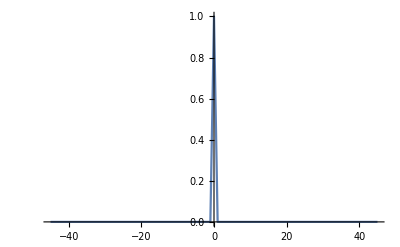

```mathematica
ListLinePlot[Table[{listx[[i]],Abs[up[listx[[i]]]]^2+Abs[down[listx[[i]]]]^2},{i,1,2pmax+1}]]  (* plot of initial probability distribution *)
```

## Coin definition

```mathematica
M = 1/Sqrt[2]*{{1,1},{-1,1}}; (* Hadamard gate *)
```

```mathematica
MatrixForm[M]
```

(1/(√2) | 1/(√2)
-1/(√2) | 1/(√2))

## Loop over time

```mathematica
unew=Table[0,{j,1,jmax+1},{p,1,2pmax+1}];
dnew=Table[0,{j,1,jmax+1},{p,1,2pmax+1}]; (* define the arrays that will get updated with every step of the walk *)
```

```mathematica
unew[[1]]= ulist ;
```

```mathematica
dnew[[1]]= dlist;
```

```mathematica
Do[
Do[
unew[[j+1,p]]=M[[1]][[1]]ulist[[p+1]]+M[[1]][[2]]dlist[[p-1]];
dnew[[j+1,p]]=M[[2]][[1]]ulist[[p+1]]+M[[2]][[2]]dlist[[p-1]]
,{p,2,2pmax}];
ulist=unew[[j+1]];dlist=dnew[[j+1]],{j,1,jmax}]
```

## Plots

### Final density

```mathematica
quantumDensity[k_] := Abs[unew[[jmax+1,k]]]^2+Abs[dnew[[jmax+1,k]]]^2;
```

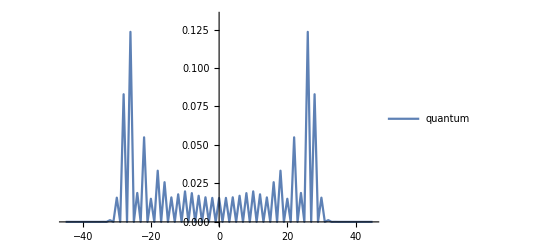

```mathematica
Image1 = ListLinePlot[
Table[{listx[[k]],quantumDensity[k]},{k,1,2pmax+1}], 
PlotRange->{All,{0,Max[Abs[unew[[jmax+1]]]^2+Abs[dnew[[jmax+1]]]^2]+0.01}},
PlotStyle->Default,
PlotLegends->Placed[LineLegend[{"quantum"}],Above]
]
```

## Classical random walk distribution

```mathematica
p=q=0.5; (* symmetrical probabilities *)
```

```mathematica
classicalDensity[k_] := jmax!/(((jmax+listx[[k]])/2)!*((jmax-listx[[k]])/2)!)*p^(0.5*(jmax+listx[[k]]))*q^(0.5*(jmax-listx[[k]]));
```

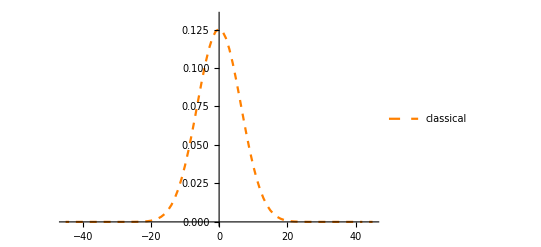

```mathematica
Image2 = ListLinePlot[
Table[{listx[[k]],classicalDensity[k]},{k,1,2pmax+1}],
PlotRange->{All,{0,Max[Abs[unew[[jmax+1]]]^2+Abs[dnew[[jmax+1]]]^2]+0.01}},
PlotStyle-> {Orange,Dashed},
PlotLegends->Placed[LineLegend[{"classical"}],Above]
]
```

## Final Plot, combined

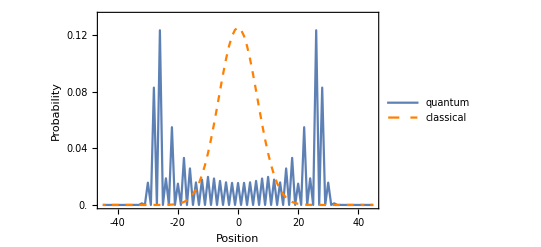

```mathematica
Show[Image1,Image2,
Axes-> None,
Frame->{{True,True},{True,True}},
FrameLabel->{"Position","Probability"},
FrameTicks->{{Range[0,0.12,0.02],Range[0,0.12,0.02]},{Range[-40,40,20],None}}
]
```

```mathematica
Rasterize[%,ImageSize->1000,ImageResolution->300]
```

-Graphics-